```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={h1>0,h2>h1};
```

```mathematica
λ[ζ_] = Exp[ζ+ⅈ π];
t[λ_]=√((λ-c^2)/(λ-1));
f0[t_]=-ⅈ h1 + h2/π(1/c Log[(t-c)/(t+c)]-Log[(t-1)/(t+1)]);
f[ζ_]=f0[t[λ[ζ]]];
```

```mathematica
(*compute derivative. Check of chain rule: *)
f0'[t[λ[ζ]]]t'[λ[ζ]]λ'[ζ] - f'[ζ]//Simplify
```

0

```mathematica
c=h2/h1;
```

```mathematica
h1=.6;
h2=1;
```

```mathematica
lim={-5h2,4h2,-.99π,0};
```

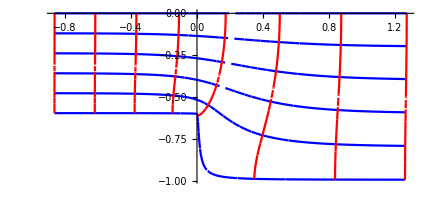

```mathematica
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]
```

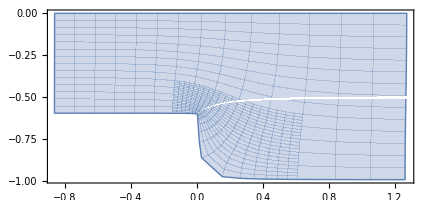

```mathematica
ParametricPlot[ReIm@f[ξ+ⅈ η],{ξ,lim⟦1⟧,lim⟦2⟧},{η,lim⟦3⟧,lim⟦4⟧}]
```

```mathematica
f[ξ]
```

(0.-0.6 ⅈ)+(-Log[(-1+√((-2.77778+ⅇ^(ⅈ π+ξ))/(-1+ⅇ^(ⅈ π+ξ))))/(1+√((-2.77778+ⅇ^(ⅈ π+ξ))/(-1+ⅇ^(ⅈ π+ξ))))]+0.6 Log[(-1.66667+√((-2.77778+ⅇ^(ⅈ π+ξ))/(-1+ⅇ^(ⅈ π+ξ))))/(1.66667+√((-2.77778+ⅇ^(ⅈ π+ξ))/(-1+ⅇ^(ⅈ π+ξ))))])/π

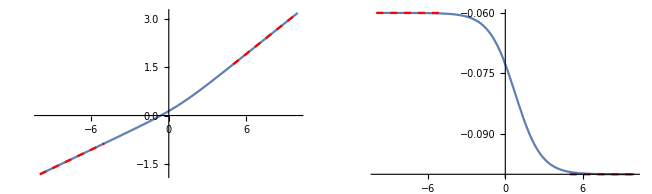

```mathematica
ξ0R = 5;ξ0L = -5;
σ = -.1π;
GraphicsRow[{
Show[{Plot[Re@f[ξ+ⅈ σ],{ξ,-10,10}],Plot[Re@f[ξ0R]+h2/π Re@ (ξ+ⅈ σ-ξ0R),{ξ,ξ0R,10},PlotStyle->{Dashed,Red}],Plot[Re@f[ξ0L]+h1/π Re@ (ξ+ⅈ σ-ξ0L),{ξ,ξ0L,-10},PlotStyle->{Dashed,Red}]}],
Show[{Plot[Im@f[ξ+ⅈ σ],{ξ,-10,10}],Plot[Im@f[ξ0R]+h2/π Im@ (ξ+ⅈ σ-ξ0R),{ξ,ξ0R,10},PlotStyle->{Dashed,Red}],Plot[Im@f[ξ0L]+h1/π Im@(ξ+ⅈ σ-ξ0L),{ξ,ξ0L,-10},PlotStyle->{Dashed,Red}]}]}]
```

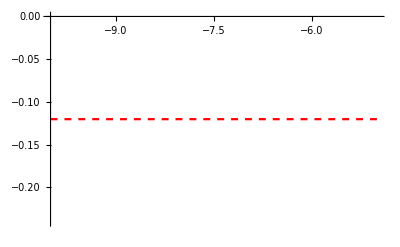

```mathematica
Plot[Im@f[ξ0L+ⅈ σ]+h1/π Im@(ξ+ⅈ σ-ξ0L),{ξ,ξ0L,-10},PlotStyle->{Dashed,Red}]
```

```mathematica
h1=.;h2=.;
Limit[t[λ[ξ+ⅈ σ]],ξ->-∞]
```

1. √(h2^2/h1^2)

Re ∑_(j=-∞)^∞ ω_j ⅇ^(ⅈ (ζ_i+ⅈ π) κ_j)  = ϕS_i, ω_-j=ω_j*
Re ω_0+Re ∑_(j=1)^∞ (ω_j ⅇ^(ⅈ (ζ_i+ⅈ π)  κ_j) +ω_j* ⅇ^(-ⅈ (ζ_i+ⅈ π)  κ_j)) = ϕS_i
Re ω_0+ ∑_(j=1)^∞ Re@ (ω_j ⅇ^(ⅈ ξ_i κ_j)ⅇ^(-(σ_i+π) κ_j) +ω_j* ⅇ^(-ⅈ ξ_i κ_j)ⅇ^((σ_i+π) κ_j)) = ϕS_i
Re ω_0+ ∑_(j=1)^∞ Re@( ω_j ⅇ^(ⅈ ξ_i κ_j))(ⅇ^(-(σ_i+π) κ_j) +ⅇ^((σ_i+π) κ_j)) = ϕS_i
Re ω_0+ ∑_(j=1)^∞ 2Re@( ω_j ⅇ^(ⅈ ξ_i κ_j))Cosh[κ_j (σ_i+π)]  = ϕS_i

```mathematica
h1=.;h2=.;
```

```mathematica
c=.;
```

```mathematica
Limit[f[ξ + ⅈ σ],ξ->-∞,Assumptions->{σ>-π, σ<0}]
```

$Aborted

```mathematica
Limit[f0[t]/Log[t-1],t->1]
```

-h2/π

-ⅈ h1+(h2 (-Log[(-1+√((ⅇ^(ⅈ π+ζ)-h2^2/h1^2)/(-1+ⅇ^(ⅈ π+ζ))))/(1+√((ⅇ^(ⅈ π+ζ)-h2^2/h1^2)/(-1+ⅇ^(ⅈ π+ζ))))]+(h1 Log[(-h2/h1+√((ⅇ^(ⅈ π+ζ)-h2^2/h1^2)/(-1+ⅇ^(ⅈ π+ζ))))/(h2/h1+√((ⅇ^(ⅈ π+ζ)-h2^2/h1^2)/(-1+ⅇ^(ⅈ π+ζ))))])/h2))/π

Derivatives :

```mathematica
dfdζ=f0'[t]t'[λ]λ'[ζ]//FullSimplify;
```

```mathematica
dfdζ=h2/(π t[λ[ζ]]);
dfdζ-f'[ζ]//FullSimplify
```

0

```mathematica
ddfdζ=-(h2 λ[ζ]t[λ[ζ]])/(2π)(c^2-1)/((λ[ζ]-c^2)^2);
ddfdζ-D[dfdζ,ζ]//FullSimplify
```

0

```mathematica
ddfdζ=-(h2 λ[ζ])/(2π t[λ[ζ]]^3)(c^2-1)/(λ[ζ]-1)^2;
ddfdζ-D[dfdζ,ζ]//FullSimplify
```

0

```mathematica
dddfdζ=(h2 λ[ζ] t[λ[ζ]]^3)/(4 π) (c^2 λ[ζ]+2 λ[ζ]^2-2 c^2-λ[ζ])(c^2-1)/((λ[ζ]-c^2)^4);
dddfdζ-D[ddfdζ,ζ]//FullSimplify
```

0

```mathematica
D[(h2 λ)/(2π)(1-c^2)/((λ-c^2)^2)√((λ-c^2)/(λ-1)),{λ,3}]//FullSimplify
```

(3 (-1+c^2) h2 (c^6 (-6+λ)+λ (-1+2 λ) (5+8 (-1+λ) λ)-3 c^4 (4+λ (-11+2 λ))+3 c^2 (-10+λ (33+4 λ (-9+2 λ)))))/(16 π (c^2-λ)^4 (-1+λ)^4 √((-c^2+λ)/(-1+λ)))